```mathematica
Ry[θ_]:=Cos[θ/2]IdentityMatrix[2]-I Sin[θ/2]PauliMatrix[2]
```

```mathematica
Rz[θ_]:=Cos[θ/2]IdentityMatrix[2]-I Sin[θ/2]PauliMatrix[3]
```

```mathematica
R[θ_,ϕ_]:=Rz[ϕ].Ry[θ]
```

```mathematica
R[θ,ϕ].{{1},{0}}
```

{{Cos[θ/2] (Cos[ϕ/2]-ⅈ Sin[ϕ/2])},{Sin[θ/2] (Cos[ϕ/2]+ⅈ Sin[ϕ/2])}}

```mathematica
Subscript[U, EQCM]={{1,0,0,0},
{0,0,√2/2,-√2/2},
{0,0,√2/2,√2/2},
{0,1,0,0}}
```

{{1,0,0,0},{0,0,1/(√2),-1/(√2)},{0,0,1/(√2),1/(√2)},{0,1,0,0}}

```mathematica
ψ=(R[θ,ϕ].{{1},{0}}ⅇ^((ⅈ ϕ)/2))⊗{{1},{0}}//FullSimplify//ArrayFlatten
```

{{Cos[θ/2]},{0},{ⅇ^(ⅈ ϕ) Sin[θ/2]},{0}}

```mathematica
x=Subscript[U, EQCM].ψ
```

{{Cos[θ/2]},{(ⅇ^(ⅈ ϕ) Sin[θ/2])/(√2)},{(ⅇ^(ⅈ ϕ) Sin[θ/2])/(√2)},{0}}

```mathematica
ρ=Simplify[x.x†,{θ,ϕ}∈Reals]
```

{{Cos[θ/2]^2,(ⅇ^(-ⅈ ϕ) Sin[θ])/(2 √2),(ⅇ^(-ⅈ ϕ) Sin[θ])/(2 √2),0},{(ⅇ^(ⅈ ϕ) Sin[θ])/(2 √2),1/2 Sin[θ/2]^2,1/2 Sin[θ/2]^2,0},{(ⅇ^(ⅈ ϕ) Sin[θ])/(2 √2),1/2 Sin[θ/2]^2,1/2 Sin[θ/2]^2,0},{0,0,0,0}}

```mathematica
ρ//MatrixForm
```

(Cos[θ/2]^2 | (ⅇ^(-ⅈ ϕ) Sin[θ])/(2 √2) | (ⅇ^(-ⅈ ϕ) Sin[θ])/(2 √2) | 0
(ⅇ^(ⅈ ϕ) Sin[θ])/(2 √2) | 1/2 Sin[θ/2]^2 | 1/2 Sin[θ/2]^2 | 0
(ⅇ^(ⅈ ϕ) Sin[θ])/(2 √2) | 1/2 Sin[θ/2]^2 | 1/2 Sin[θ/2]^2 | 0
0 | 0 | 0 | 0)

```mathematica
PartialTrace[r_]:=Map[Tr,Partition[r,{2,2}],{2}]
```

```mathematica
PartialTrace[ρ]
```

{{Cos[θ/2]^2+1/2 Sin[θ/2]^2,(ⅇ^(-ⅈ ϕ) Sin[θ])/(2 √2)},{(ⅇ^(ⅈ ϕ) Sin[θ])/(2 √2),1/2 Sin[θ/2]^2}}

```mathematica
y=R[θ,ϕ].{{1},{0}}
```

{{Cos[θ/2] (Cos[ϕ/2]-ⅈ Sin[ϕ/2])},{Sin[θ/2] (Cos[ϕ/2]+ⅈ Sin[ϕ/2])}}

```mathematica
F=Simplify[y†.PartialTrace[ρ].y,{θ,ϕ}∈Reals]//Simplify
```

{{1/8 (5+√2+2 Cos[θ]-(-1+√2) Cos[2 θ])}}

```mathematica
F/.θ->π/2//Simplify
```

{{1/4 (2+√2)}}

```mathematica
1/(4π)Integrate[F Sin[θ],{θ,0,π},{ϕ,0,2π}]
```

{{1/12 (7+2 √2)}}

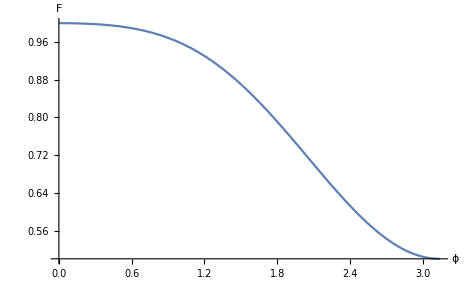

```mathematica
Plot[F,{θ,0,π},AxesLabel->{"ϕ","F"}]
```

```mathematica
Show[%85,PlotLabel->None,LabelStyle->{14,GrayLevel[0],Bold}]
```

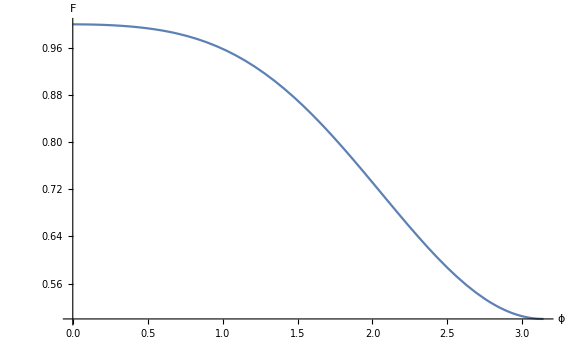

```mathematica
Show[%86,ImageSize->Large]
```

```mathematica
1/(4π)Integrate[F^2 Sin[θ],{θ,0,π},{ϕ,0,2π}]
```

{{1/60 (26+11 √2)}}

```mathematica
√(1/60 (26+11 √2)-(1/12 (7+2 √2))^2)//Simplify//N
```

0.147603

```mathematica
F/.θ->π
```

{{1/2}}

```mathematica
PartialTrace[ρ,2,2,1]//TrigReduce
```

{{1/4 (3+Cos[θ]),(ⅇ^(-ⅈ ϕ) Sin[θ])/(2 √2)},{(ⅇ^(ⅈ ϕ) Sin[θ])/(2 √2),1/4 (1-Cos[θ])}}

```mathematica
PartialTrace[ρ,2,2,2]//TrigReduce
```

{{1/4 (3+Cos[θ]),(ⅇ^(-ⅈ ϕ) Sin[θ])/(2 √2)},{(ⅇ^(ⅈ ϕ) Sin[θ])/(2 √2),1/4 (1-Cos[θ])}}

```mathematica
a=1/(√2){{1},{1}};b=1/(√2){{1},{-1}};
```

```mathematica
T=ArrayFlatten[(a⊗b)].ArrayFlatten[(a⊗b)]†
```

{{1/4,-1/4,1/4,-1/4},{-1/4,1/4,-1/4,1/4},{1/4,-1/4,1/4,-1/4},{-1/4,1/4,-1/4,1/4}}

```mathematica
PartialTrace[T,2,2,1]
```

{{1/2,-1/2},{-1/2,1/2}}

```mathematica
PartialTrace[T,2,2,2]
```

{{1/2,1/2},{1/2,1/2}}

```mathematica
w=1/(√2){{1},{Exp[I ϕ]}}
```

```mathematica
z={{1/(√2)},{ⅇ^(ⅈ ϕ)/(√2)Cos[α]},{ⅇ^(ⅈ ϕ)/(√2)Sin[α]},{0}}
```

{{1/(√2)},{(ⅇ^(ⅈ ϕ) Cos[α])/(√2)},{(ⅇ^(ⅈ ϕ) Sin[α])/(√2)},{0}}

```mathematica
Simplify[z.z†,{α,ϕ}∈Reals]
```

{{1/2,1/2 ⅇ^(-ⅈ ϕ) Cos[α],1/2 ⅇ^(-ⅈ ϕ) Sin[α],0},{1/2 ⅇ^(ⅈ ϕ) Cos[α],Cos[α]^2/2,1/4 Sin[2 α],0},{1/2 ⅇ^(ⅈ ϕ) Sin[α],1/4 Sin[2 α],Sin[α]^2/2,0},{0,0,0,0}}

```mathematica
PartialTrace[Simplify[z.z†,{α,ϕ}∈Reals],2,2,1]
```

{{1/2+Sin[α]^2/2,1/2 ⅇ^(-ⅈ ϕ) Cos[α]},{1/2 ⅇ^(ⅈ ϕ) Cos[α],Cos[α]^2/2}}

```mathematica
PartialTrace[Simplify[z.z†,{α,ϕ}∈Reals],2,2,2]
```

{{1/2+Cos[α]^2/2,1/2 ⅇ^(-ⅈ ϕ) Sin[α]},{1/2 ⅇ^(ⅈ ϕ) Sin[α],Sin[α]^2/2}}

```mathematica
Simplify[w†.{{1/2+Sin[α]^2/2,1/2 ⅇ^(-ⅈ ϕ) Cos[α]},{1/2 ⅇ^(ⅈ ϕ) Cos[α],Cos[α]^2/2}}.w,{α,ϕ}∈Reals]//TrigReduce
```

{{1/2 (1+Cos[α])}}

```mathematica
Simplify[w†.{{1/2+Cos[α]^2/2,1/2 ⅇ^(-ⅈ ϕ) Sin[α]},{1/2 ⅇ^(ⅈ ϕ) Sin[α],Sin[α]^2/2}}.w,{α,ϕ}∈Reals]//TrigReduce
```

{{1/2 (1+Sin[α])}}